1.1.1 Excersise 1

```mathematica
data=Import["C:\\Users\\JSTASTNY\\Downloads\TEK001.CSV","CSV"]
```

{{-0.005,1.8},{-0.004996,2},{-0.004992,2.2},{-0.004988,2.2},{-0.004984,2.6},{-0.00498,2.8},{-0.004976,3.2},{-0.004972,3.2},{-0.004968,3.4},{-0.004964,3.6},{-0.00496,3.8},{-0.004956,3.8},{-0.004952,4.2},{-0.004948,4.2},{-0.004944,4.4},{-0.00494,4.4},{-0.004936,4.6},{-0.004932,4.6},{-0.004928,4.8},{-0.004924,4.8},{-0.00492,5},{-0.004916,5},{-0.004912,5},{-0.004908,5},{-0.004904,5},{-0.0049,5},{-0.004896,5},{-0.004892,5},2445,{0.004892,-4.4},{0.004896,-4.2},{0.0049,-4.2},{0.004904,-4},{0.004908,-3.6},{0.004912,-3.6},{0.004916,-3.2},{0.00492,-3.2},{0.004924,-3},{0.004928,-2.8},{0.004932,-2.4},{0.004936,-2.4},{0.00494,-2.2},{0.004944,-1.8},{0.004948,-1.6},{0.004952,-1.4},{0.004956,-1},{0.00496,-0.8},{0.004964,-0.6},{0.004968,-0.4},{0.004972,-0.2},{0.004976,0.2},{0.00498,0.4},{0.004984,0.6},{0.004988,0.8},{0.004992,1.2},{0.004996,1.6}}
 |  |  |  |

```mathematica
time=data[[All,1]];
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

```mathematica
volts=data[[All,2]];
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

```mathematica
window=Table[(0.5)*(1-Cos[(2*Pi(n-1))/(2500)]), {n,2500}];
```

```mathematica
w=window*volts;
```

```mathematica
data1=Transpose[{time,w}]
```

{{-0.005,0.},{-0.004996,3.15827×10^-6},{-0.004992,0.0000138964},{-0.004988,0.0000312668},{-0.004984,0.0000656915},{-0.00498,0.000110538},{-0.004976,0.000181913},{-0.004972,0.000247602},{-0.004968,0.000343609},{-0.004964,0.000460457},{-0.00496,0.00060004},{-0.004956,0.000726041},{-0.004952,0.000954989},2474,{0.004948,-0.000426961},{0.004952,-0.00031833},{0.004956,-0.000191063},{0.00496,-0.000126324},{0.004964,-0.0000767428},{0.004968,-0.0000404245},{0.004972,-0.0000154751},{0.004976,0.0000113696},{0.00498,0.0000157912},{0.004984,0.0000151596},{0.004988,0.0000113697},{0.004992,7.57984×10^-6},{0.004996,2.52662×10^-6}}
 |  |  |  |

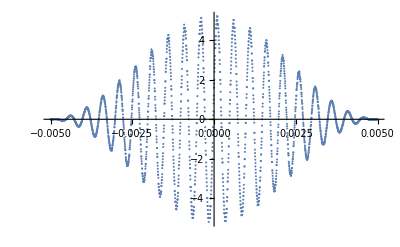

```mathematica
ListPlot[data1]
```

1.1.2 Exercise 2

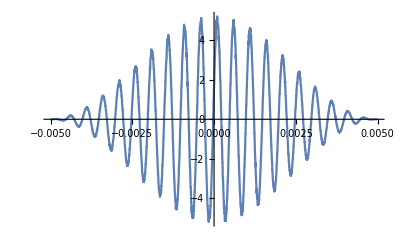

```mathematica
a=ListPlot[data1,Joined->True]
```

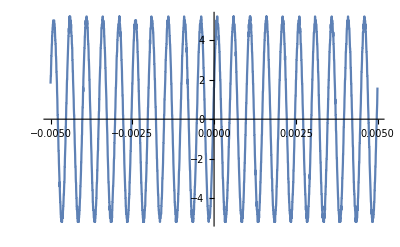

```mathematica
b=ListPlot[data,Joined->True]
```

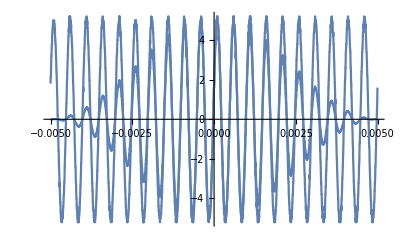

```mathematica
zplot=Show[a,b]
```

1.1.3 Exercise 3

```mathematica
Export["C:\\Users\\JSTASTNY\\Dropbox\\School Work\\UNG 2017\\Modern Physics\\Hann.pdf",zplot,"PDF"]
```

C:\Users\JSTASTNY\Dropbox\School Work\UNG 2017\Modern Physics\Hann.pdf

1.1.4 Exercise 4

```mathematica
Export["C:\\Users\\JSTASTNY\\Dropbox\\School Work\\UNG 2017\\Modern Physics\\Unwindowed.txt",data,"Text"]
```

C:\Users\JSTASTNY\Dropbox\School Work\UNG 2017\Modern Physics\Unwindowed.txt